```mathematica
rawdata=Import["/Users/WillC/Documents/Rutgers/Research/RADICAL/minions/concurrencytest.csv"][[All,All]];
core1=rawdata[[1;;2]]
core2=rawdata[[3;;7]]
core4=rawdata[[8;;12]]
(*rawdata=Table[{rawdata[[x,2]],rawdata[[x,1]]},{x,1,Length[rawdata]}]*)
```

{{1,1,300.011},{1,2,599.994}}

{{2,1,300.003},{2,2,300.002},{2,4,599.989},{2,8,1199.96},{2,16,2399.93}}

{{4,1,300.},{4,2,300.001},{4,4,300.003},{4,8,599.994},{4,16,1199.98}}

#### Linear Fit

```mathematica
lm = LinearModelFit[avgPoints,x,x];
Normal[lm]
```

```mathematica
Normal[lm]
```

86.0805-10.4321 x

```mathematica
standardError[ts_]:=StandardDeviation[ts]/Abs[ts]
```

```mathematica
stderr=standardError[avgPoints[[All,2]]]
stderr=Table[{avgPoints[[i,1]],avgPoints[[i,2]],stderr[[i]]},{i,1,3}]
```

{0.211747,0.242451,0.360908}

{{1,75.2895,0.211747},{2,65.7549,0.242451},{4,44.1728,0.360908}}

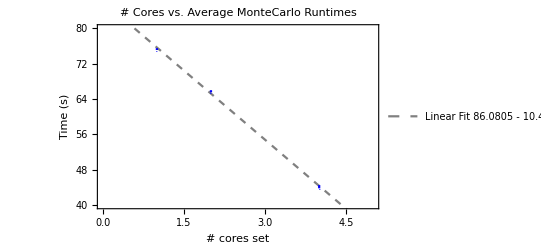

```mathematica
points=ListPlot[avgPoints,PlotRange->{{0,5},All},PlotMarkers->{Automatic,Small},PlotStyle->{Black,Opacity[0.5]}];

fit=Plot[lm[x],{x,0,5},PlotStyle->{Gray,Dashed},PlotLegends->{"Linear Fit\n"<>ToString[Normal[lm]], FontSize->12}];

Needs["ErrorBarPlots`"]
errplot=ErrorListPlot[stderr,PlotMarkers->{".",Tiny},PlotStyle->{Blue}];

final=Show[{fit,errplot(*,points*)},Frame->True,FrameLabel->{"# cores set","Time (s)"},LabelStyle->Bold,PlotLabel->"# Cores vs. Average MonteCarlo Runtimes",PlotRange->{All,{40,80}}]
```

```mathematica
Rasterize[final,ImageResolution->200]
```

-Graphics-